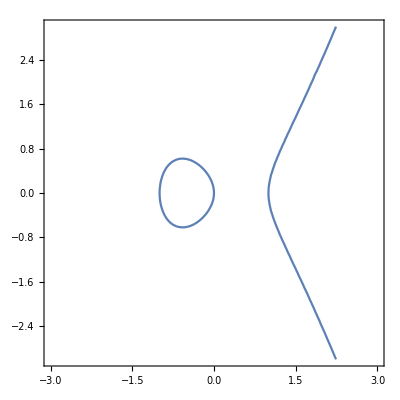

```mathematica
p1 = ContourPlot[y^2==x(x-1)(x+1),{x,-3,3},{y,-3,3},Axes->True]
```

```mathematica
k = Sqrt[6]/3
```

√(2/3)

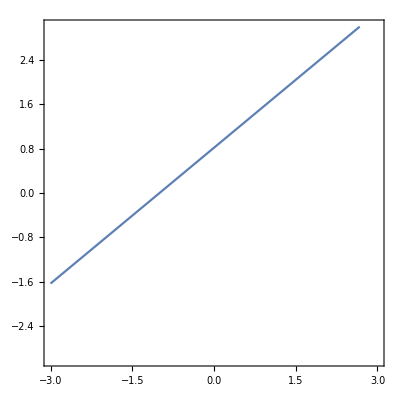

```mathematica
p2 = ContourPlot[y==k*x+k,{x,-3,3},{y,-3,3},Axes->True]
```

```mathematica
p3 = Graphics[{PointSize[0.02],Point[{-1,0}]}]
```

-Graphics-

```mathematica
p4 = Graphics[{PointSize[0.02],Point[{2,Sqrt[6]}]}]
```

-Graphics-

```mathematica
p5 = Graphics[{PointSize[0.02],Point[{-1/3,(2 √(2/3))/3}]}]
```

-Graphics-

```mathematica
p6 = Graphics[{PointSize[0.02],Point[{-1/3,-(2*Sqrt[6])/9}]}]
```

-Graphics-

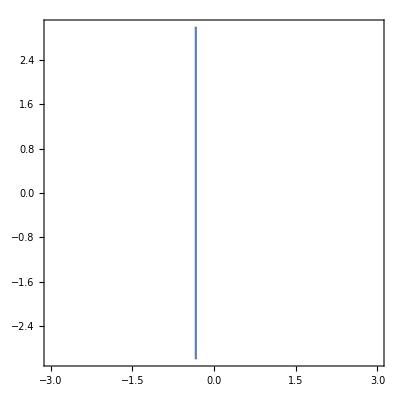

```mathematica
p7 = ContourPlot[x==-1/3,{x,-3,3},{y,-3,3},Axes->True]
```

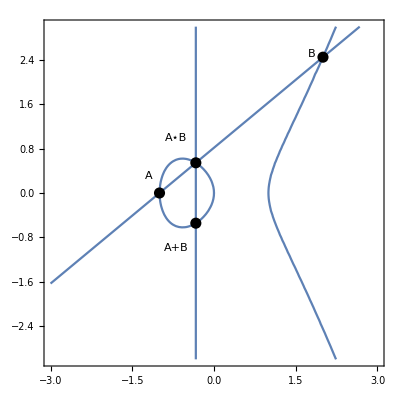

```mathematica
Show[p1,p2,p7,{p3,Graphics[Text[A,{-1.2,0.3}]]},{p4,Graphics[Text[B,{1.8,2.5}]]},{p5,Graphics[Text[A⋆B,{-0.7,1}]]},{p6,Graphics[Text[A+B,{-0.7,-1}]]}]
```

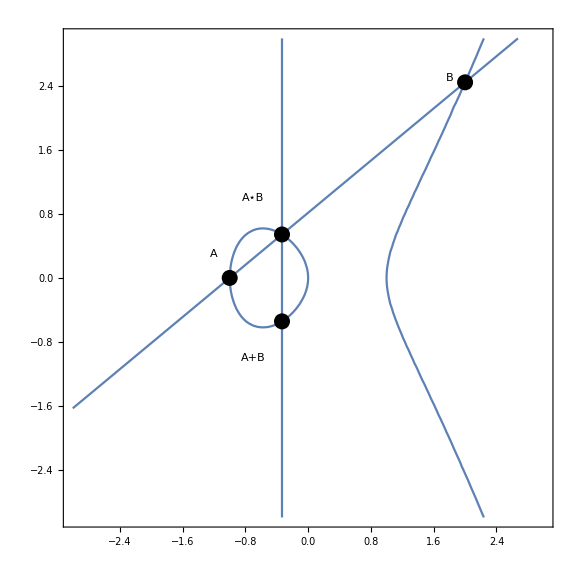

```mathematica
Show[%14,ImageSize->Large]
```

```mathematica
Solve[{y^2-x^3+x ==0,y== k*x+k},{x,y}]
```

{{x→-1,y→0},{x→-1/3,y→(2 √(2/3))/3},{x→2,y→√6}}